# Scattering Kernels in 3D

This is code to accompany the book:
A Hitchhiker’s Guide to Multiple Scattering
© 2020 Eugene d’Eon 
www.eugenedeon.com/hitchhikers

## Callisto

[Porco et al. 2008] - doi: 10.1088/0004-6256/136/5/2172

```mathematica
pCallisto[u_]:=HeavisideTheta[2.521-ArcCos[-u]] 2.2/(4 Pi (1.0004369822233856))(2-0.79333 ArcCos[-u]+Exp[-21.2 ArcCos[-u]])(1+Sin[ArcCos[-u]/2]Tan[ArcCos[-u]/2]Log[Tan[ArcCos[-u]/4]])
```

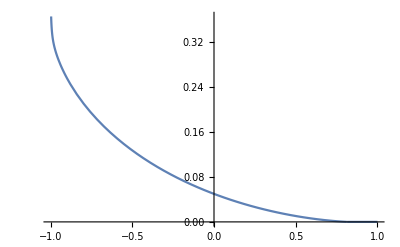

```mathematica
Plot[pCallisto[u],{u,-1,1}]
```

### Normalization condition

```mathematica
NIntegrate[ 2 Pi pCallisto[u],{u,-1,1}]
```

1.

### Mean cosine (g)

```mathematica
NIntegrate[2 Pi pCallisto[u]u,{u,-1,1}]
```

-0.560001

### Legendre expansion coefficients

```mathematica
NIntegrate[2Pi(2k+1)pCallisto[Cos[y]]LegendreP[k,Cos[y]]Sin[y]/.k->0,{y,0,Pi}]
```

1.

```mathematica
NIntegrate[2Pi(2k+1)pCallisto[Cos[y]]LegendreP[k,Cos[y]]Sin[y]/.k->1,{y,0,Pi}]
```

-1.68

```mathematica
NIntegrate[2Pi(2k+1)pCallisto[Cos[y]]LegendreP[k,Cos[y]]Sin[y]/.k->2,{y,0,Pi}]
```

0.851712

```mathematica
NIntegrate[2Pi(2k+1)pCallisto[Cos[y]]LegendreP[k,Cos[y]]Sin[y]/.k->3,{y,0,Pi}]
```

-0.285211

```mathematica
NIntegrate[2Pi(2k+1)pCallisto[Cos[y]]LegendreP[k,Cos[y]]Sin[y]/.k->4,{y,0,Pi}]
```

0.182995

```mathematica
NIntegrate[2Pi(2k+1)pCallisto[Cos[y]]LegendreP[k,Cos[y]]Sin[y]/.k->6,{y,0,Pi}]
```

0.0908047

```mathematica
NIntegrate[2Pi(2k+1)pCallisto[Cos[y]]LegendreP[k,Cos[y]]Sin[y]/.k->8,{y,0,Pi}]
```

0.064234

```mathematica
NIntegrate[2Pi(2k+1)pCallisto[Cos[y]]LegendreP[k,Cos[y]]Sin[y]/.k->10,{y,0,Pi}]
```

0.0552028